## 导入数据

```mathematica
SetDirectory["C:\\Users\\Rick\\Desktop\\FundModel\\DFFC-FundModel\\csv_data"];
data10=Reverse[Drop[Import["017437.csv"],1]ᵀ[[3]]ᵀ];
data1=Table[{i,data10[[i]]},{i,-Length[data10],-1}];
datadate1=Drop[Import["017437.csv"],1]ᵀ[[2]];
```

```mathematica
SlidingAverage[arr_,window_Integer]:=Module[{n,half},
n=Length[arr];
half=Floor[window/2];
Table[With[{start=Max[1,i-half],end=Min[n,i+half]},Mean[arr[[start;;end]]]],{i,1,n}]]
```

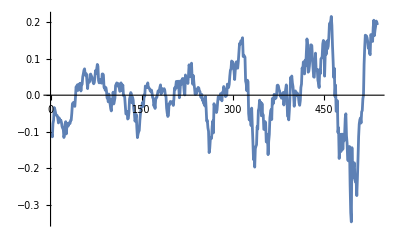

```mathematica
ListLinePlot[data1ᵀ[[2]]-SlidingAverage[data1ᵀ[[2]],100]]
```

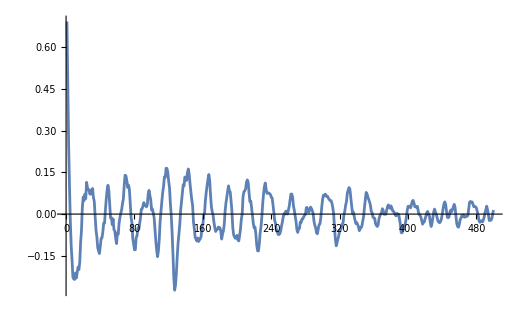

```mathematica
codata=Table[CorrelationFunction[data1ᵀ[[2]]-SlidingAverage[data1ᵀ[[2]],20],i],{i,1,500}];
ListLinePlot[codata,PlotRange->Full]
```

```mathematica
res=Table[codata=Table[CorrelationFunction[data1ᵀ[[2]]-SlidingAverage[data1ᵀ[[2]],j],i],{i,1,200}];
{j,FindPeaks[-codata,2][[1,1]]},{j,2,50}]
```

{{2,1},{3,1},{4,2},{5,2},{6,3},{7,3},{8,4},{9,4},{10,5},{11,5},{12,5},{13,5},{14,6},{15,6},{16,6},{17,6},{18,8},{19,8},{20,10},{21,10},{22,12},{23,12},{24,12},{25,12},{26,12},{27,12},{28,13},{29,13},{30,13},{31,13},{32,15},{33,15},{34,15},{35,15},{36,15},{37,15},{38,15},{39,15},{40,16},{41,16},{42,16},{43,16},{44,16},{45,16},{46,16},{47,16},{48,16},{49,16},{50,18}}

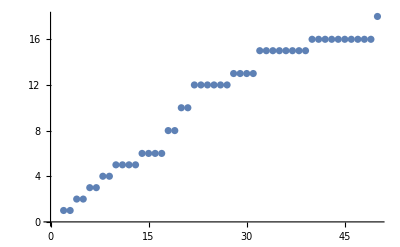

```mathematica
ListPlot[res]
```

```mathematica
splitAtZeroCrossings[list_]:=Module[{signChanges,splitIndices},signChanges=Flatten@Position[Abs[Differences[Sign[list]]],_?(#!=0&)];
splitIndices=Prepend[signChanges+1,1];
Split[list,Abs[#2]>0&&Sign[#1]==Sign[#2]&]]
```

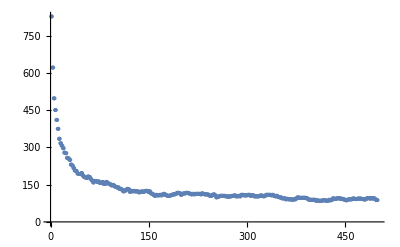

```mathematica
Table[Abs[Length@splitAtZeroCrossings[data1ᵀ[[2]]-SlidingAverage[data1ᵀ[[2]],i]]],{i,2,500}];
ListPlot[%,PlotRange->Full]
```

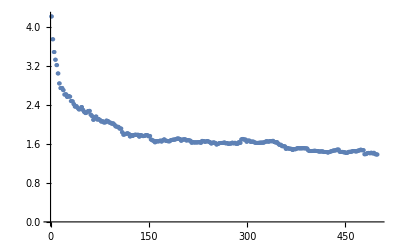

```mathematica
Table[Abs[Mean/@splitAtZeroCrossings[data1ᵀ[[2]]-SlidingAverage[data1ᵀ[[2]],i]]]//Total,{i,2,500}];
ListPlot[%,PlotRange->Full]
```

## Peaks

```mathematica
peaksup0=FindPeaks[data1ᵀ[[2]],2];
peaksdown0=FindPeaks[-data1ᵀ[[2]],2];
pkup=Table[data1[[Floor[peaksup0[[i,1]]]]],{i,Length@peaksup0}];
pkdown=Table[data1[[Floor[peaksdown0[[i,1]]]]],{i,Length@peaksdown0}];
```

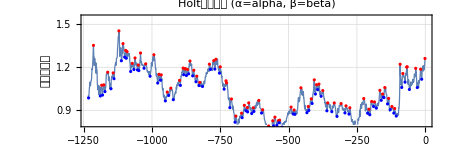

```mathematica
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListPlot[{pkup,pkdown},PlotStyle->{{Red,PointSize[0.005]},{Blue,PointSize[0.005]}}],ImageSize->450
]
```

7.89103

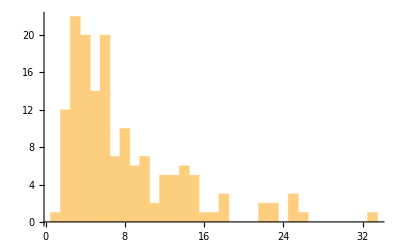

```mathematica
Differences[Flatten[{pkupᵀ[[1]],pkdownᵀ[[1]]},1]//Sort]//Mean//N
Histogram[Differences[Flatten[{pkupᵀ[[1]],pkdownᵀ[[1]]},1]//Sort],60]
```

## 时间序列预测 holt-winter

```mathematica
HoltRollingPredict[data_,α_,β_]:=Module[{times,values,n,levels,trends,forecasts,predSteps=1},{times,values}=Transpose[data];
n=Length[times];
levels=ConstantArray[0.,n];
trends=ConstantArray[0.,n];
forecasts=ConstantArray[0.,n];
levels[[1]]=values[[1]];
trends[[1]]=If[n>1,values[[2]]-values[[1]],0];
Do[If[i>1,levels[[i]]=α*values[[i]]+(1-α)*(levels[[i-1]]+trends[[i-1]]);
trends[[i]]=β*(levels[[i]]-levels[[i-1]])+(1-β)*trends[[i-1]]];
If[i<n,forecasts[[i+1]]=levels[[i]]+trends[[i]]*predSteps],{i,1,n}
];
Transpose[{times,forecasts}]
];
```

### 计算举例+可视化

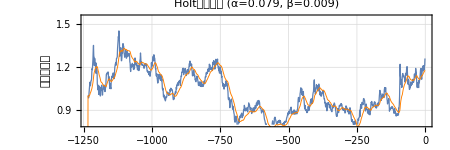

```mathematica
(*手动调节参数*)
alpha=0.079;  (*水平平滑因子，建议范围0.1-0.5*)
beta=0.009;   (*趋势平滑因子，建议范围0.05-0.3*)
result=HoltRollingPredict[data1,alpha,beta];
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[result,PlotStyle->{Orange,Thickness[0.0015]}],ImageSize->450
]
```

### 涨落天数可视化

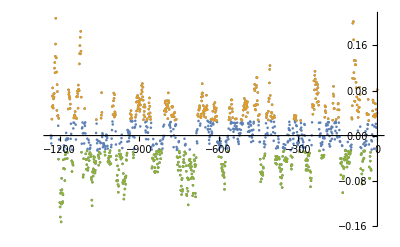

```mathematica
deltadata={data1ᵀ[[1]],data1ᵀ[[2]]-resultᵀ[[2]]}ᵀ;
thres=0.45;
pkdelta=Cases[deltadata,u_/;Abs[u[[2]]]>thres*StandardDeviation[deltadataᵀ[[2]]]];
pkindexup=Cases[pkdelta,u_/;u[[2]]>0]ᵀ[[1]];
pkindexdown=Cases[pkdelta,u_/;u[[2]]<0]ᵀ[[1]];
ListPlot[{deltadata,deltadata[[pkindexup]],deltadata[[pkindexdown]]}]
```

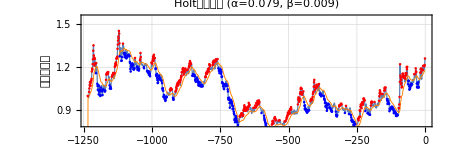

```mathematica
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[result,PlotStyle->{Orange,Thickness[0.0015]}],
ListPlot[{data1[[pkindexup]],data1[[pkindexdown]]},AspectRatio->1/3,PlotStyle->{{Red,PointSize[0.004]},{Blue,PointSize[0.004]}}],
ImageSize->450
]
```

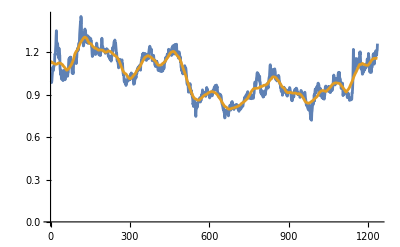

```mathematica
ListLinePlot[{data1ᵀ[[2]],EstimatedBackground[data1ᵀ[[2]],Method->"MovingAverage"]}]
```

```mathematica
back=EstimatedBackground[data1ᵀ[[2]],Method->"MovingAverage"];
res=Table[
resul1t=HoltRollingPredict[data1,α,β]ᵀ[[2]];
a=back[[-700;;-1]];
b=resul1t[[-700;;-1]];
{α,β,Mean[(a-b)^2]},
{α,0.06,0.1,0.001},{β,0.001,0.02,0.001}];
```

```mathematica
MinimalBy[Flatten[res,1],Last]
```

{{0.091,0.001,0.000878472}}

```mathematica
colorlist={RGBColor["#47bd96"],RGBColor["#ee3b68"],RGBColor["#479bd3"],RGBColor["#755ca2"],RGBColor["#e38922"],Gray};
```

```mathematica
SlidingAverage[arr_,window_Integer]:=Module[{n,half},
n=Length[arr];
half=Floor[window/2];
Table[With[{start=Max[1,i-half],end=Min[n,i+half]},Mean[arr[[start;;end]]]],{i,1,n}]]
```

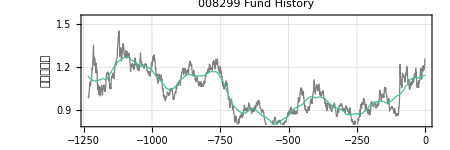

```mathematica
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{colorlist[[-1]],PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style["008299 Fund History",12]
],
ListLinePlot[{data1[[;;,1]],SlidingAverage[data1ᵀ[[2]],80]}ᵀ,AspectRatio->1/3,PlotStyle->{colorlist[[1]],PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style["008299 Fund History",14]
],ImageSize->450
]
```

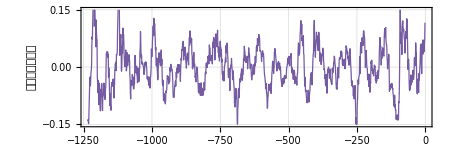

```mathematica
Show[
ListLinePlot[{data1[[;;,1]],data1[[;;,2]]-SlidingAverage[data1ᵀ[[2]],80]}ᵀ,AspectRatio->1/3,PlotStyle->{colorlist[[4]],PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.15,-0.15}},FrameLabel->{"交易日（天）","波动净值（元）"},
Axes->True
],ImageSize->450
]
```

## 对涨落的导数（动量）的分析

```mathematica
difdelta={deltadataᵀ[[1]],ExponentialMovingAverage[#,0.2]&@({0}~Join~Differences@(deltadataᵀ[[2]]))}ᵀ;
```

```mathematica
stddif=StandardDeviation[difdeltaᵀ[[2]]]
```

0.0111522

选择标准：
	1. 超过阈值
	2. 动量小于阈值（在某一个动量平滑参数优化下）

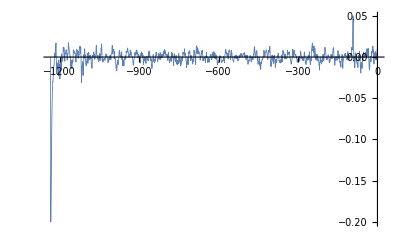

```mathematica
ListLinePlot[{difdelta},PlotStyle->{Thickness[0.0015]},PlotRange->Full]
```

```mathematica
lessmomentum=Cases[difdelta,u_/;Abs[u[[2]]]<0.5stddif]ᵀ[[1]];
pkindexupa=Cases[pkindexup,u_/;MemberQ[lessmomentum,u]];
pkindexdowna=Cases[pkindexdown,u_/;MemberQ[lessmomentum,u]];
```

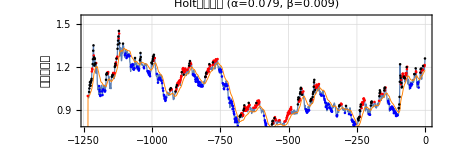

```mathematica
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[result,PlotStyle->{Orange,Thickness[0.0015]}],
ListPlot[{data1[[pkindexupa]],data1[[pkindexdowna]]},AspectRatio->1/3,PlotStyle->{{Red,PointSize[0.004]},{Blue,PointSize[0.004]}}],
ListPlot[{data1[[DeleteCases[pkindexup,u_/;MemberQ[pkindexupa,u]]]],DeleteCases[pkindexdown,u_/;MemberQ[pkindexdowna,u]]},AspectRatio->1/3,PlotStyle->{{Black,PointSize[0.004]},{Black,PointSize[0.004]}}],
ImageSize->450
]
```

## 三参数+季节性holtwinters

```mathematica
HoltWintersRollingPredict[data_,α_,β_,γ_,seasonLength_,predSteps_:1]:=Module[{times,values,n,levels,trends,seasonals,forecasts},{times,values}=Transpose[data];(*分离时间和数值*)n=Length[times];(*数据长度*)(*初始化水平、趋势、季节性分量和预测值*)levels=ConstantArray[0.,n];
trends=ConstantArray[0.,n];
seasonals=ConstantArray[0.,n];
forecasts=ConstantArray[0.,n];
(*初始水平、趋势和季节性分量的估计*)levels[[1]]=values[[1]];
trends[[1]]=If[n>1,values[[2]]-values[[1]],0];
seasonals[[1;;seasonLength]]=values[[1;;seasonLength]]-levels[[1]];
(*滚动预测*)Do[If[i>seasonLength,(*更新水平、趋势和季节性分量*)levels[[i]]=α (values[[i]]-seasonals[[i-seasonLength]])+(1-α) (levels[[i-1]]+trends[[i-1]]);
trends[[i]]=β (levels[[i]]-levels[[i-1]])+(1-β) trends[[i-1]];
seasonals[[i]]=γ (values[[i]]-levels[[i]])+(1-γ) seasonals[[i-seasonLength]];];
(*预测未来值*)If[i<n,forecasts[[i+1]]=levels[[i]]+trends[[i]]*predSteps+seasonals[[i+1-seasonLength]];],{i,1,n}];
(*返回时间和预测值的列表*)Transpose[{times,forecasts}]]
```

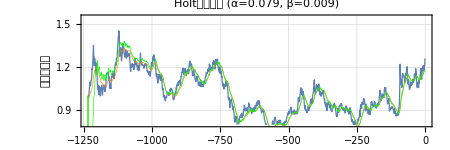

```mathematica
(*手动调节参数*)
alpha=0.079;  (*水平平滑因子，建议范围0.1-0.5*)
beta=0.009;   (*趋势平滑因子，建议范围0.05-0.3*)
γ=0.1;
seasonLength=7;
result3=HoltWintersRollingPredict[data1,alpha,beta,γ,seasonLength];
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.8,1.55}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[{result,result3},PlotStyle->{{Orange,Thickness[0.001]},{Green,Thickness[0.001]}}],ImageSize->450
]
```

## 涨落的优化

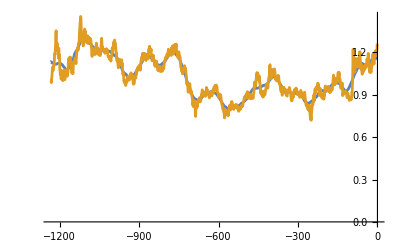

```mathematica
ListLinePlot[{{data1ᵀ[[1]],EstimatedBackground[data1ᵀ[[2]],Method->"MovingAverage"]}ᵀ,data1}]
```

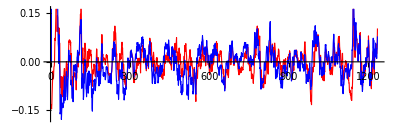

```mathematica
ListLinePlot[{data1ᵀ[[2]]-EstimatedBackground[data1ᵀ[[2]],Method->"MovingAverage"],data1ᵀ[[2]]-result3ᵀ[[2]]},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},AspectRatio->1/3]
```

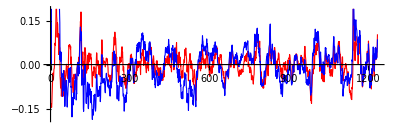

```mathematica
result4=HoltWintersRollingPredict[data1,0.05,0.01,0.04,9];
ListLinePlot[{data1ᵀ[[2]]-EstimatedBackground[data1ᵀ[[2]],Method->"MovingAverage"],data1ᵀ[[2]]-result4ᵀ[[2]]},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},AspectRatio->1/3]
```

```mathematica
result3[[-10;;-1]]
```

{{-10,1.143},{-9,1.14583},{-8,1.15158},{-7,1.1596},{-6,1.1583},{-5,1.1702},{-4,1.17306},{-3,1.17225},{-2,1.17448},{-1,1.18273}}

## 参数稳定性

```mathematica
paradata=Import["holtwinters_results1.csv"];
```

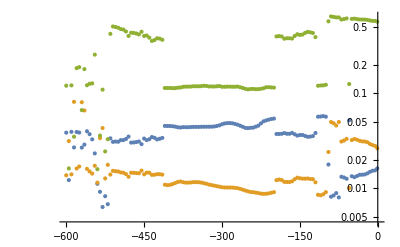

```mathematica
parasortdata=Sort[paradata[[2;;-1]]];
ListLogPlot[{parasortdata[[;;,{1,2}]],parasortdata[[;;,{1,3}]],parasortdata[[;;,{1,4}]]},PlotRange->Full]
```

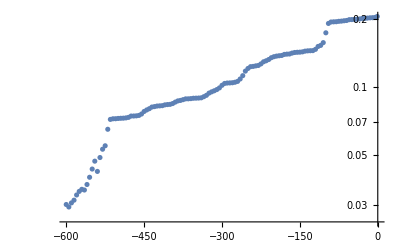

```mathematica
ListLogPlot[{parasortdata[[;;,{1,6}]]},PlotRange->Full]
```

```mathematica
SlidingAverage[arr_,window_Integer]:=Module[{n,half},
n=Length[arr];
half=Floor[window/2];
Table[With[{start=Max[1,i-half],end=Min[n,i+half]},Mean[arr[[start;;end]]]],{i,1,n}]]
```

```mathematica
meandata={data1ᵀ[[1]],SlidingAverage[data1,20]ᵀ[[2]]}ᵀ;
flucdata={data1ᵀ[[1]],data1ᵀ[[2]]-SlidingAverage[data1,20]ᵀ[[2]]}ᵀ;
```

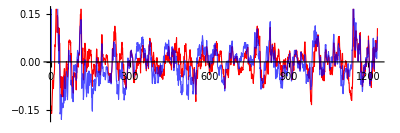

```mathematica
ListLinePlot[{flucdataᵀ[[2]],data1ᵀ[[2]]-result3ᵀ[[2]]},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002],Opacity[0.7]}},AspectRatio->1/3]
```

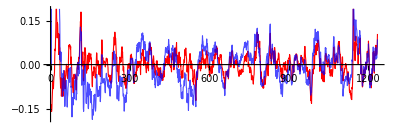

```mathematica
result4=HoltWintersRollingPredict[data1,0.05,0.01,0.04,9];
ListLinePlot[{flucdataᵀ[[2]],(data1ᵀ[[2]]-result4ᵀ[[2]])},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002],Opacity[0.7]}},AspectRatio->1/3]
```

## 波动统计和关联和方差分析

```mathematica
SetDirectory[NotebookDirectory[]]
<<"PLOT.wl"
```

C:\Users\Rick\Desktop\FundModel\MMA-holtwintercheck

colorlist::shdw: 符号 colorlist 出现在多个上下文 {PLOT`,Global`} 中；上下文 PLOT` 中的定义可能遮蔽或者被其他定义遮蔽.

```mathematica
hlist[h_]:=
{Table[(h⟦1,i⟧+h⟦1,i-1⟧)/2,{i,2,Length[h⟦1⟧]}],Table[(h⟦1,i⟧-h⟦1,i-1⟧)^-1*h⟦2,i-1⟧,{i,2,Length[h⟦1⟧]}]*Length[(Table[(h⟦1,i⟧-h⟦1,i-1⟧)^-1*h⟦2,i-1⟧,{i,2,Length[h⟦1⟧]}])]/Total[(Table[(h⟦1,i⟧-h⟦1,i-1⟧)^-1*h⟦2,i-1⟧,{i,2,Length[h⟦1⟧]}])]/((h⟦1,Length[h⟦1⟧]⟧+h⟦1,Length[h⟦1⟧]-1⟧)/2-(h⟦1,2⟧+h⟦1,2-1⟧)/2)};
```

```mathematica
hlist[HistogramList[flucdataᵀ[[2]]]]
```

{{-31/200,-29/200,-27/200,-1/8,-23/200,-21/200,-19/200,-17/200,-3/40,-13/200,-11/200,-9/200,-7/200,-1/40,-3/200,-1/200,1/200,3/200,1/40,7/200,9/200,11/200,13/200,3/40,17/200,19/200,21/200,23/200,1/8,27/200,29/200,31/200,33/200,7/40,37/200,39/200,41/200,43/200,9/40},{30/361,60/361,90/361,120/361,120/361,210/361,180/361,450/361,510/361,780/361,1290/361,2430/361,2550/361,3150/361,3270/361,3450/361,3870/361,3240/361,2940/361,2880/361,1350/361,1290/361,870/361,510/361,390/361,330/361,210/361,90/361,60/361,60/361,90/361,60/361,0,30/361,30/361,0,30/361,0,30/361}}

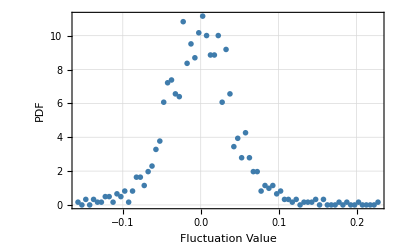

```mathematica
listplot[{{Null},hlist[HistogramList[flucdataᵀ[[2]],60]]ᵀ},GridLines->Automatic,Axes->True,FrameLabel->{"Fluctuation Value","PDF"}]
```

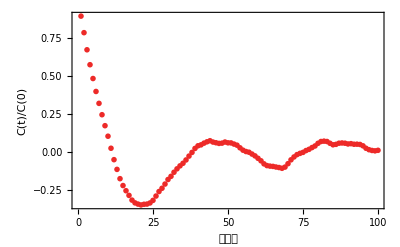

```mathematica
listplot[CorrelationFunction[flucdataᵀ[[2]],{1,100,1}],PlotRange->Full,Axes->True,FrameLabel->{"交易日","C(t)/C(0)"}]
```

### 基本不相关

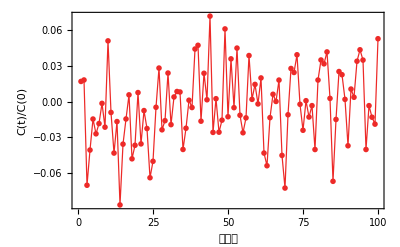

```mathematica
Differences[flucdataᵀ[[2]]];
listplot[CorrelationFunction[%,{1,100,1}],PlotRange->Full,Axes->True,FrameLabel->{"交易日","C(t)/C(0)"},Joined->True]
```

```mathematica
codata={Range[40],CorrelationFunction[flucdataᵀ[[2]],{1,40}]}ᵀ;
```

{γ→0.0496001,ω→0.13347}

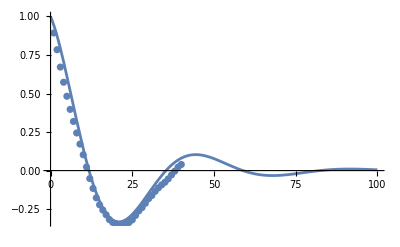

```mathematica
ClearAll[a,b,
γ,
ω,co]
re=FindFit[codata, ⅇ^(-γ  t)Cos[ω t],{γ,ω},t]
co[t_]:=ⅇ^(-γ t)Cos[ω t];
Show[Plot[co[x]/.re,{x,0,100},PlotRange->Full],
ListPlot[codata]]
```

```mathematica
0.053140143976075443*2
```

0.10628

```mathematica
0.148834^2+0.053140143976075443^2
```

0.0249754

0.01

Part::take: 无法在 virtual1 中提取位置 27 至 100.

Part::take: 无法在 virtual2 中提取位置 101 至 159.

Part::take: 无法在 virtual1 中提取位置 160 至 199.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+{-0.0764477,0.118205,-0.0779024,«5»,-0.404476,-0.215927,«48»} 中长度不相等的对象无法合并.

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+{«1»}+{-0.0764477,0.118205,-0.0779024,«5»,-0.404476,-0.215927,«48»} 中长度不相等的对象无法合并.

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+«1»+«1»+{0.0170862,-0.070095,0.0425053,«5»,-0.0499637,-0.135598,«11»} 中长度不相等的对象无法合并.

General::stop: 在本次计算中，Thread::tdlen 的进一步输出将被抑制.

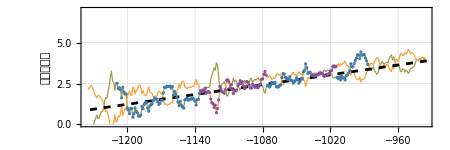

```mathematica
a=0.01
re2={Differences[virtual1[[27;;100,2]]],
Differences[virtual2[[101;;159,2]]],
Differences[virtual1[[160;;199,2]]],
Differences[virtual2[[200;;221,2]]],
Differences[virtual1[[222;;249,2]]]}//Flatten//Accumulate;
co2=Table[{i-1198,re2[[i]]},{i,1,Length@re2}];
virtual1=Table[{flucdata[[i,1]],1+a i +9flucdataᵀ[[2,i]]},{i,1,300}];
virtual2=Table[{flucdata[[i,1]],1+a i -8flucdataᵀ[[2,i]]+0.1RandomReal[]},{i,1,300}];
Show[
ListLinePlot[{virtual1,virtual2},AspectRatio->1/3,PlotStyle->{{colorlist[[4]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",PlotRange->{Full,{0,7}},FrameLabel->{"交易日（天）","净值（元）"}
],Plot[1+a (x+1223),{x,-1233,-850},PlotStyle->{Dashed,Black}],
ListPlot[virtual1[[27;;100]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],
ListPlot[virtual1[[160;;199]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],
ListPlot[virtual1[[222;;249]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],ListPlot[virtual2[[101;;159]],PlotStyle->{colorlist[[5]],PointSize[0.005]}],
ListPlot[virtual2[[200;;221]],PlotStyle->{colorlist[[5]],PointSize[0.005]}],

ListLinePlot[co2,PlotStyle->{colorlist[[6]],PointSize[0.005]}],
ImageSize->450
]
```

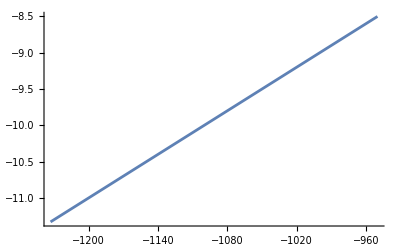

```mathematica
Plot[1+a x,{x,-1233,-950}]
```

0.01

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+{-0.0764477,0.118205,-0.0779024,«5»,-0.404476,-0.215927,«48»} 中长度不相等的对象无法合并.

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+{«1»}+{-0.0764477,0.118205,-0.0779024,«5»,-0.404476,-0.215927,«48»} 中长度不相等的对象无法合并.

Thread::tdlen: {-0.324641,0.0532353,-0.116847,-0.503847,0.644535,-0.290265,-0.120359,0.0097,-0.852906,-0.130612,«63»}+«1»+«1»+{0.0170862,-0.070095,0.0425053,«5»,-0.0499637,-0.135598,«11»} 中长度不相等的对象无法合并.

General::stop: 在本次计算中，Thread::tdlen 的进一步输出将被抑制.

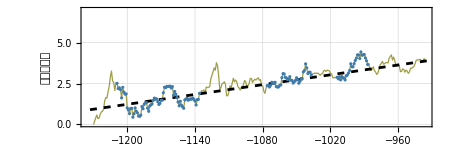

```mathematica
a=0.01
re1={Differences[virtual1[[27;;100,2]]],
Table[0,{i,1,61}],
Differences[virtual1[[160;;199,2]]],
Table[0,{i,1,24}],
Differences[virtual1[[222;;249,2]]]}//Flatten//Accumulate;
co1=Table[{i-1198,re1[[i]]},{i,1,Length@re2}];
Show[
ListLinePlot[{virtual1},AspectRatio->1/3,PlotStyle->{{colorlist[[4]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",PlotRange->{Full,{0,7}},FrameLabel->{"交易日（天）","净值（元）"}
],Plot[1+a (x+1223),{x,-1233,-850},PlotStyle->{Dashed,Black}],
ListPlot[virtual1[[27;;100]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],
ListPlot[virtual1[[160;;199]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],
ListPlot[virtual1[[222;;249]],PlotStyle->{colorlist[[2]],PointSize[0.005]}],

ListLinePlot[co1,PlotStyle->{colorlist[[6]],PointSize[0.005]}],
ImageSize->450
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
csvdir="C:\\Users\\Rick\\Desktop\\FundModel\\choosefund\\csv_data\\"
data10=Reverse[Drop[Import[csvdir<>"015877.csv"],1]ᵀ[[3]]ᵀ];
data1=Table[{i,data10[[i]]},{i,-Length[data10],-1}];
datadate1=Drop[Import[csvdir<>"015877.csv"],1]ᵀ[[2]];
data20=Reverse[Drop[Import[csvdir<>"015686.csv"],1]ᵀ[[3]]ᵀ];
data2=Table[{i,data20[[i]]},{i,-Length[data20],-1}];
datadate2=Drop[Import[csvdir<>"015686.csv"],1]ᵀ[[2]];
```

C:\Users\Rick\Desktop\FundModel\choosefund\csv_data\

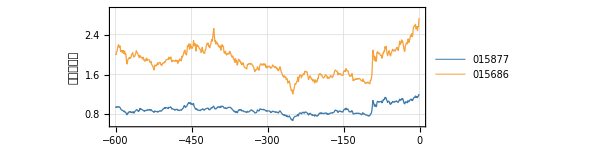

```mathematica
Show[
ListLinePlot[{data1[[-600;;-1]],data2[[-600;;-1]]},AspectRatio->1/3,PlotStyle->{{colorlist[[2]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",PlotRange->{Full,{0.6,2.9}},FrameLabel->{"交易日（天）","净值（元）"},PlotLegends->Placed[{"015877","015686"},Right]
],ImageSize->450
]
```

```mathematica
flucco1={data1[[-600;;-1,1]],data1[[-600;;-1,2]]-SlidingAverage[data1,50][[-600;;-1,2]]}ᵀ;
flucco2={data2[[-600;;-1,1]],data2[[-600;;-1,2]]-SlidingAverage[data2,50][[-600;;-1,2]]}ᵀ;
```

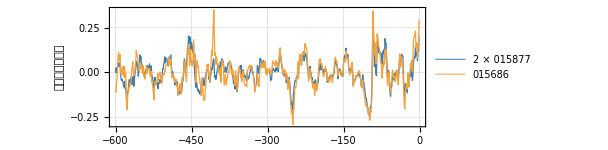

```mathematica
Show[
ListLinePlot[{{flucco1ᵀ[[1]],flucco1ᵀ[[2]]*2}ᵀ,flucco2},AspectRatio->1/3,PlotStyle->{{colorlist[[2]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",PlotRange->{Full,Full},FrameLabel->{"交易日（天）","波动净值（元）"},
Axes->True,PlotLegends->Placed[{"2 × 015877","015686"},Right]
],ImageSize->450
]
```

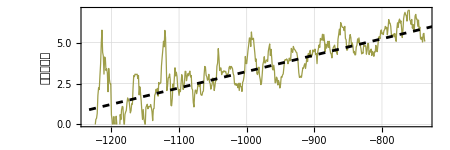

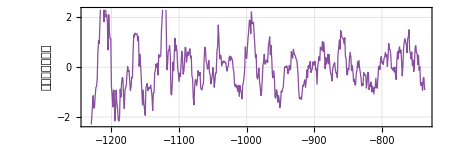

```mathematica
virtual01=Table[{flucdata[[i,1]],1+a i +20flucdataᵀ[[2,i]]},{i,1,500}];
virtual01fluc=Table[{flucdata[[i,1]],20flucdataᵀ[[2,i]]},{i,1,500}];
Show[
ListLinePlot[{virtual01},AspectRatio->1/3,PlotStyle->{{colorlist[[4]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",PlotRange->{Full,{0,7}},FrameLabel->{"交易日（天）","净值（元）"}
],Plot[1+a (x+1223),{x,-1233,-250},PlotStyle->{Dashed,Black}],
ImageSize->450
]

ListLinePlot[{virtual01fluc},AspectRatio->1/3,PlotStyle->{{colorlist[[5]],PointSize[0.1],Thickness[0.002]},{colorlist[[3]],PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",FrameLabel->{"交易日（天）","波动净值（元）"},Axes->True,PlotRange->{Full,{-2.3,2.3}}
]
```

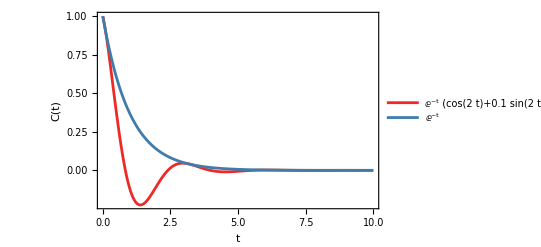

```mathematica
plot[{ⅇ^(-t)(Cos[2t]+0.1Sin[2t]),ⅇ^(-t)},{t,0,10},PlotRange->Full,PlotLegends->"Expressions",Axes->True,FrameLabel->{"t","C(t)"}]
```